```mathematica
<<NeuralNetworks`
```

```mathematica
resource=ResourceObject["MNIST"];trainingData=ResourceData[resource,"TrainingData"];testData=ResourceData[resource,"TestData"];
```

```mathematica
trainingData[[1;;5,1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomSample[trainingData,5]
```

{-Graphics-→5,-Graphics-→6,-Graphics-→8,-Graphics-→9,-Graphics-→1}

```mathematica
lenet=NetChain[{ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,10,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",Range[0,9]}],"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]]
```

```mathematica
lenet1 = NetChain[{ConvolutionLayer[20,5]},"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}],"Output"-> NetDecoder[{"Image"}]]
lenet1 = NetInitialize[lenet1,"Xavier"]
lenet1=NetTrain[lenet1,trainingData,ValidationSet->testData];
```

```mathematica
enc = NetEncoder[{"Image",{28,28},"Grayscale"}]
```

NetEncoder[<>]

```mathematica
lenet1=NetInitialize[lenet[[1]],"Xavier"];
ArrayPlot[lenet1@enc[trainingData[[1,1]]][[1]]]
```

ConvolutionLayer::invindata1: Data supplied to port "Input" was a 28×28 matrix, but expected a 1×28×28 3-tensor.

ArrayPlot::mat: Argument $Failed at position 1 is not a list of lists.

ArrayPlot[$Failed]

```mathematica
lenetLayers = {ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,10} (*,SoftmaxLayer[]}*);
```

```mathematica
netTable = Table[NetInitialize[NetChain[lenetLayers[[1;;i]],"Input"->NetEncoder[{"Image",28}],"Output"->Automatic],"Xavier"],{i,Length[lenetLayers]}];
```

```mathematica
Table[netTable[[i]][trainingData[[1;;10,1]]],{i,2}]
```

### </NB: This is interesting.

```mathematica
Table[Table[Image[netTable[[i]][dataPoint],Magnification->4,ColorSpace->"Grayscale"],{dataPoint,trainingData[[1;;10,1]]}],{i,4}]
```

Image::imgcsmis: The specified color space Grayscale and the number of channels 24 are not compatible.

General::stop: Further output of Image::imgcsmis will be suppressed during this calculation.

{1}
 |  |  |  |

### NB/>

```mathematica
Table[Image[im],{im,netTable[[1]][trainingData[[1,1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Table[Table[Image[out,Magnification->4],{out,netTable[[i]][dataPoint]}],{dataPoint,trainingData[[1;;10,1]]}],{i,4}]
```

```mathematica
Table[Image[netTable[[i]][trainingData[[1;;10,1]]],Magnification->4],{i,2}]
```

Image::imgarray: The specified argument {{«1»},«8»,{«1»}} should be an array of rank 2 or 3 with machine-sized numbers.

Image::imgarray: The specified argument {«1»} should be an array of rank 2 or 3 with machine-sized numbers.

{Image[{1},Magnification→4],Image[{{1},{1},{1},{1},{{1},18,{1}},{{1},18,{1}},{1},{{1},19},{1},{1}},Magnification→4]}
 |  |  |  |

```mathematica
Table[Image[netTable[[i]][trainingData[[1;;10,1]]],Magnification->4],{i,Length[netTable]}]
```

Image::imgarray: The specified argument {{«1»},«8»,{«1»}} should be an array of rank 2 or 3 with machine-sized numbers.

Image::imgarray: The specified argument {«1»} should be an array of rank 2 or 3 with machine-sized numbers.

General::stop: Further output of Image::imgarray will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
Table[Image[ImageAdjust@netTable[[1]]@image,Magnification->4],{image,trainingData[[1;;100,1]]}]
```

ImageAdjust::imginv: Expecting an image or graphics instead of {«1»}.

Image::imgarray: The specified argument ImageAdjust[{«1»}] should be an array of rank 2 or 3 with machine-sized numbers.

ImageAdjust::imginv: Expecting an image or graphics instead of {{{-2.64212,-2.64212,-2.64212,-2.64212,-2.64212,-2.64212,-2.64212,«10»,-2.35669,-1.99364,-2.21378,-2.55497,-2.64212,-2.64212,-2.64212},«22»,{-«19»,«22»,-«19»}},«19»}.

Image::imgarray: The specified argument ImageAdjust[{{{-2.64212,-2.64212,-2.64212,-2.64212,-2.64212,-2.64212,-2.64212,«10»,-2.35669,-1.99364,-2.21378,-2.55497,-2.64212,-2.64212,-2.64212},«22»,{«1»}},«19»}] should be an array of rank 2 or 3 with machine-sized numbers.

ImageAdjust::imginv: Expecting an image or graphics instead of {«1»}.

General::stop: Further output of ImageAdjust::imginv will be suppressed during this calculation.

Image::imgarray: The specified argument ImageAdjust[{«1»}] should be an array of rank 2 or 3 with machine-sized numbers.

General::stop: Further output of Image::imgarray will be suppressed during this calculation.

{Image[ImageAdjust[{1}],Magnification→4],Image[ImageAdjust[{1}],Magnification→4],Image[ImageAdjust[{{1},18,{{1},22,{1}}}],1],94,1,Image[ImageAdjust[{1}],Magnification→4],Image[ImageAdjust[{1}],Magnification→4]}
 |  |  |  |

```mathematica
net = NetChain[{ConvolutionLayer[2,3],Ramp, ConvolutionLayer[3,3],Ramp},"Input"->NetEncoder[{"Image",28}],"Output"->"Image"]
```

NetChain[]

```mathematica
netInit= NetInitialize[net,"Xavier"]
```

NetChain[]

```mathematica
Dynamic[Image[ImageAdjust@netInit@trainingData[[1,1]],Magnification->4]]
```

```mathematica
lenet = NetInitialize[lenet,"Xavier"]
```

NetChain[]

```mathematica
NetExtract[lenet,All]
```

{ConvolutionLayer[<>],ElementwiseLayer[<>],PoolingLayer[<>],ConvolutionLayer[<>],ElementwiseLayer[<>],PoolingLayer[<>],FlattenLayer[<>],LinearLayer[<>],ElementwiseLayer[<>],LinearLayer[<>],SoftmaxLayer[<>]}

```mathematica
lenet=NetTrain[lenet,trainingData,ValidationSet->testData,MaxTrainingRounds->3];
```

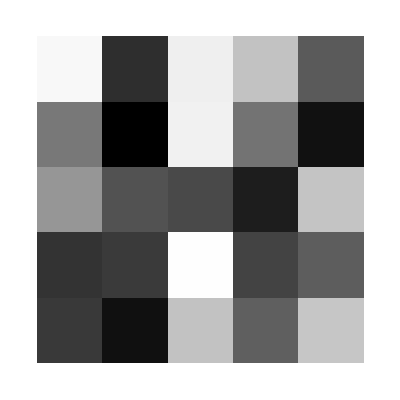

```mathematica
ArrayPlot[NetExtract[lenet[[1]],"Weights"][[1]][[1]]]
```

```mathematica
ArrayPlot[{NetExtract[lenet[[1]],"Weights"]}]
```

-Graphics-

```mathematica
numUnits[layer_] := Length[NetExtract[lenet[[layer]],"Weights"]]
```

## Filters at Conv Layers

```mathematica
Table[Table[ArrayPlot[NetExtract[lenet[[layer]],"Weights"][[i]][[1]],ImageSize->(2000/numUnits[layer])],{i,1,numUnits[layer]}],{layer,{1,4}}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Partition[Image[Partition[#/Max[Abs[#]],28],ColorSpace->"Grayscale"]&/@NetExtract[lenet,{1,"Weights"}],5]//Grid
```

Image::imgarray: The specified argument {} should be an array of rank 2 or 3 with machine-sized numbers.

General::stop: Further output of Image::imgarray will be suppressed during this calculation.

Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale]
Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale]
Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale]
Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale] | Image[{},ColorSpace→Grayscale]

```mathematica
f
```

## NetChain Scratchwork

```mathematica
net = NetChain
```

```mathematica
NetInitialize[NetGraph[{BatchNormalizationLayer[],Tanh,LogisticSigmoid,Tanh,TotalLayer[],TotalLayer[],TotalLayer[],CatenateLayer[],DotPlusLayer[50],BatchNormalizationLayer[],Tanh,LogisticSigmoid,Tanh,TotalLayer[],TotalLayer[],TotalLayer[],CatenateLayer[],DotPlusLayer[50],DropoutLayer[],DropoutLayer[],TotalLayer[],LogisticSigmoid,BatchNormalizationLayer[],Tanh,LogisticSigmoid,Tanh,TotalLayer[],TotalLayer[],TotalLayer[],CatenateLayer[],DotPlusLayer[50],DropoutLayer[],TotalLayer[],TotalLayer[],TotalLayer[],TotalLayer[],TotalLayer[],TotalLayer[],DotPlusLayer[50],DotPlusLayer[1]},{1->2,1->3,1->4,2->5,3->5,3->6,4->6,2->7,4->7,5->8,6->8,7->8,8->9,10->11,10->12,10->13,11->14,12->14,11->15,13->15,13->16,12->16,16->17,15->17,14->17,17->18,18->19,9->20,20->21,19->21,21->22,23->24,23->25,23->26,24->27,25->27,24->28,25->29,26->28,26->29,27->30,28->30,29->30,30->31,31->32,32->21,30->33,8->33,8->34,17->34,30->35,17->35,33->36,34->36,34->37,35->37,37->38,36->38,38->39,39->21,22->40},"Input"->85]]
```

NetGraph[]

```mathematica
Table[{Dimensions[NetInitialize[ConvolutionLayer[1,{i,j},"Input"->{3,3,3}]][{{{1,2,3},{3,2,1},{7,8,9}},{{4,5,6},{6,5,4},{1,2,3}},{{7,8,9},{9,8,7},{4,5,6}}}]],NetInitialize[ConvolutionLayer[1,{i,j},"Input"->{3,3,3}]][{{{1,2,3},{3,2,1},{7,8,9}},{{4,5,6},{6,5,4},{1,2,3}},{{7,8,9},{9,8,7},{4,5,6}}}]},{i,1,3},{j,1,3}]//MatrixForm
```

(({1,3,3}
{{{-0.613938,-0.433453,-0.252969},{-0.252969,-0.433453,-0.613938},{0.276481,0.456965,0.63745}}}) | ({1,3,2}
{{{0.617246,0.526037},{1.12441,1.21561},{-3.54867,-3.63988}}}) | ({1,3,1}
{{{-9.1897},{-6.76847},{0.331927}}})
({1,2,3}
{{{7.41657,6.31563,5.2147},{7.87808,8.97901,10.0799}}}) | ({1,2,2}
{{{5.97678,4.23415},{-0.463672,1.27895}}}) | ({1,2,1}
{{{-7.42226},{-5.52212}}})
({1,1,3}
{{{-0.628012,-1.55364,-2.47927}}}) | ({1,1,2}
{{{0.54561,-0.177972}}}) | ({1,1,1}
{{{8.32105}}}))